```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
controlColor=Black;
```

```mathematica
v1Color=Blend[{RGBColor["#ff1f5b"],Green},0.25];
```

```mathematica
lpColor=Blend[{RGBColor["#009ade"],Green},0.25];
```

```mathematica
lmColor=Blend[{RGBColor["#f28522"],Green},0.25];
```

```mathematica
(*************************)
```

```mathematica
dateMouseListControl={{"011622","Mouse22550"},{"011822","Mouse22550"},{"012322","Mouse22549"},{"012622","Mouse22549"},{"021022","Mouse22549"},{"010522","Mouse22599"},{"021022","Mouse22599"},{"021422","Mouse22599"},{"033122","Mouse22544"},{"040122","Mouse22562"},{"040322","Mouse22544"},{"040322","Mouse22562"}};
```

```mathematica
(***V1 axons, eOPN3***)
```

```mathematica
dateMouseListV1axons={{"112221","Mouse22485"},{"112321","Mouse22485"},{"120321","Mouse22485"},{"120821","Mouse22517"},{"121321","Mouse22485"},{"010122","Mouse22547"},{"011222","Mouse22501"},{"011622","Mouse22504"},{"011822","Mouse22504"},{"012322","Mouse22575"},{"012722","Mouse22575"},{"013122","Mouse22504"},{"021022","Mouse22504"},{"021222","Mouse22575"},{"032222","Mouse22506"},{"032622","Mouse22506"},{"040422","Mouse22506"}};
```

```mathematica
(***LP axons, eOPN3***)
```

```mathematica
dateMouseListLPaxons={{"020122","Mouse22413"},{"020922","Mouse22413"},{"021422","Mouse22413"},{"012622","Mouse22514"},{"012822","Mouse22514"},{"020122","Mouse22514"},{"021122","Mouse22519"},{"021122","Mouse22535"},{"021522","Mouse22535"},{"021722","Mouse22519"},{"030122","Mouse22513"},{"030222","Mouse22521"},{"030722","Mouse22513"},{"030822","Mouse22521"},{"030822","Mouse22519"},{"031522","Mouse22513"},{"031522","Mouse22521"},{"031922","Mouse22521"},{"032022","Mouse22519"},{"032222","Mouse22513"},{"040622","Mouse22513"}};
```

```mathematica
(***LM axons, eOPN3***)
```

```mathematica
dateMouseListLMaxons={{"022022","Mouse22563"},{"022222","Mouse22563"},{"031722","Mouse22539"},{"031722","Mouse22570"},{"032022","Mouse22539"},{"032022","Mouse22570"},{"032322","Mouse22539"},{"032522","Mouse22539"},{"041022","Mouse22407"},{"041522","Mouse22407"}};
```

```mathematica
(****************************)
```

```mathematica
pairedROIsControl=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_pairedROIs.txt"],"List"],{n,1,Length[dateMouseListControl]}];
```

```mathematica
pairedROIsV1axons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_pairedROIs.txt"],"List"],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
pairedROIsLPaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_pairedROIs.txt"],"List"],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
pairedROIsLMaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_pairedROIs.txt"],"List"],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
(*****************************)
```

```mathematica
normCRFsBeforeControl=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_normCRFbefore_ROI",ToString[i],".txt"],"List"],{i,pairedROIsControl[[n]]}],{n,1,Length[dateMouseListControl]}];
```

```mathematica
normCRFsBeforeControlYs=Table[Table[Part[#,2]&/@normCRFsBeforeControl[[m,n]],{n,1,Length[normCRFsBeforeControl[[m]]]}],{m,1,Length[normCRFsBeforeControl]}];
```

```mathematica
normCRFsAfterControl=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_normCRFafter_ROI",ToString[i],".txt"],"List"],{i,pairedROIsControl[[n]]}],{n,1,Length[dateMouseListControl]}];
```

```mathematica
normCRFsAfterControlYs=Table[Table[Part[#,2]&/@normCRFsAfterControl[[m,n]],{n,1,Length[normCRFsAfterControl[[m]]]}],{m,1,Length[normCRFsAfterControl]}];
```

```mathematica
(*****************************)
```

```mathematica
normCRFsBeforeV1axons=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_normCRFbefore_ROI",ToString[i],".txt"],"List"],{i,pairedROIsV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
normCRFsBeforeV1axonsYs=Table[Table[Part[#,2]&/@normCRFsBeforeV1axons[[m,n]],{n,1,Length[normCRFsBeforeV1axons[[m]]]}],{m,1,Length[normCRFsBeforeV1axons]}];
```

```mathematica
normCRFsAfterV1axons=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_normCRFafter_ROI",ToString[i],".txt"],"List"],{i,pairedROIsV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
normCRFsAfterV1axonsYs=Table[Table[Part[#,2]&/@normCRFsAfterV1axons[[m,n]],{n,1,Length[normCRFsAfterV1axons[[m]]]}],{m,1,Length[normCRFsAfterV1axons]}];
```

```mathematica
(*****************************)
```

```mathematica
normCRFsBeforeLPaxons=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_normCRFbefore_ROI",ToString[i],".txt"],"List"],{i,pairedROIsLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
normCRFsBeforeLPaxonsYs=Table[Table[Part[#,2]&/@normCRFsBeforeLPaxons[[m,n]],{n,1,Length[normCRFsBeforeLPaxons[[m]]]}],{m,1,Length[normCRFsBeforeLPaxons]}];
```

```mathematica
normCRFsAfterLPaxons=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_normCRFafter_ROI",ToString[i],".txt"],"List"],{i,pairedROIsLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
normCRFsAfterLPaxonsYs=Table[Table[Part[#,2]&/@normCRFsAfterLPaxons[[m,n]],{n,1,Length[normCRFsAfterLPaxons[[m]]]}],{m,1,Length[normCRFsAfterLPaxons]}];
```

```mathematica
(*****************************)
```

```mathematica
normCRFsBeforeLMaxons=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_normCRFbefore_ROI",ToString[i],".txt"],"List"],{i,pairedROIsLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
normCRFsBeforeLMaxonsYs=Table[Table[Part[#,2]&/@normCRFsBeforeLMaxons[[m,n]],{n,1,Length[normCRFsBeforeLMaxons[[m]]]}],{m,1,Length[normCRFsBeforeLMaxons]}];
```

```mathematica
normCRFsAfterLMaxons=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_normCRFafter_ROI",ToString[i],".txt"],"List"],{i,pairedROIsLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
normCRFsAfterLMaxonsYs=Table[Table[Part[#,2]&/@normCRFsAfterLMaxons[[m,n]],{n,1,Length[normCRFsAfterLMaxons[[m]]]}],{m,1,Length[normCRFsAfterLMaxons]}];
```

```mathematica
(*********************************)
```

```mathematica
meanNormCRFBeforeControl=Mean[Flatten[normCRFsBeforeControlYs,1]];
```

```mathematica
semNormCRFBeforeControl=StandardDeviation[Flatten[normCRFsBeforeControlYs,1]]/Sqrt[Length[Flatten[normCRFsBeforeControlYs,1]]];
```

```mathematica
(***)
```

```mathematica
meanNormCRFAfterControl=Mean[Flatten[normCRFsAfterControlYs,1]];
```

```mathematica
semNormCRFAfterControl=StandardDeviation[Flatten[normCRFsAfterControlYs,1]]/Sqrt[Length[Flatten[normCRFsAfterControlYs,1]]];
```

```mathematica
(*********************************)
```

```mathematica
meanNormCRFBeforeV1axons=Mean[Flatten[normCRFsBeforeV1axonsYs,1]];
```

```mathematica
semNormCRFBeforeV1axons=StandardDeviation[Flatten[normCRFsBeforeV1axonsYs,1]]/Sqrt[Length[Flatten[normCRFsBeforeV1axonsYs,1]]];
```

```mathematica
(***)
```

```mathematica
meanNormCRFAfterV1axons=Mean[Flatten[normCRFsAfterV1axonsYs,1]];
```

```mathematica
semNormCRFAfterV1axons=StandardDeviation[Flatten[normCRFsAfterV1axonsYs,1]]/Sqrt[Length[Flatten[normCRFsAfterV1axonsYs,1]]];
```

```mathematica
(*********************************)
```

```mathematica
meanNormCRFBeforeLPaxons=Mean[Flatten[normCRFsBeforeLPaxonsYs,1]];
```

```mathematica
semNormCRFBeforeLPaxons=StandardDeviation[Flatten[normCRFsBeforeLPaxonsYs,1]]/Sqrt[Length[Flatten[normCRFsBeforeLPaxonsYs,1]]];
```

```mathematica
(***)
```

```mathematica
meanNormCRFAfterLPaxons=Mean[Flatten[normCRFsAfterLPaxonsYs,1]];
```

```mathematica
semNormCRFAfterLPaxons=StandardDeviation[Flatten[normCRFsAfterLPaxonsYs,1]]/Sqrt[Length[Flatten[normCRFsAfterLPaxonsYs,1]]];
```

```mathematica
(*********************************)
```

```mathematica
meanNormCRFBeforeLMaxons=Mean[Flatten[normCRFsBeforeLMaxonsYs,1]];
```

```mathematica
semNormCRFBeforeLMaxons=StandardDeviation[Flatten[normCRFsBeforeLMaxonsYs,1]]/Sqrt[Length[Flatten[normCRFsBeforeLMaxonsYs,1]]];
```

```mathematica
(***)
```

```mathematica
meanNormCRFAfterLMaxons=Mean[Flatten[normCRFsAfterLMaxonsYs,1]];
```

```mathematica
semNormCRFAfterLMaxons=StandardDeviation[Flatten[normCRFsAfterLMaxonsYs,1]]/Sqrt[Length[Flatten[normCRFsAfterLMaxonsYs,1]]];
```

```mathematica
(****************************************************************)
```

```mathematica
contrastList={10,15,22,32,46,68,100};
```

```mathematica
(*****************************************)
```

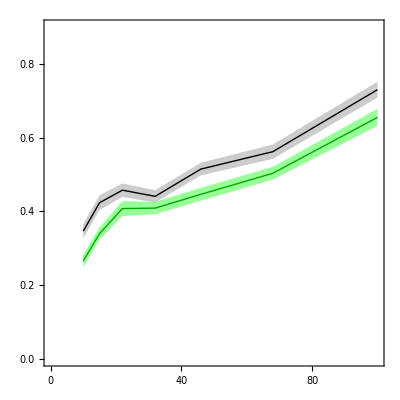

```mathematica
Show[ListLinePlot[{Partition[Riffle[contrastList,meanNormCRFBeforeControl],2],Partition[Riffle[contrastList,(meanNormCRFBeforeControl+semNormCRFBeforeControl)],2],Partition[Riffle[contrastList,(meanNormCRFBeforeControl-semNormCRFBeforeControl)],2]},PlotRange->{0,0.9},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,100,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick],ListLinePlot[{Partition[Riffle[contrastList,meanNormCRFAfterControl],2],Partition[Riffle[contrastList,(meanNormCRFAfterControl+semNormCRFAfterControl)],2],Partition[Riffle[contrastList,(meanNormCRFAfterControl-semNormCRFAfterControl)],2]},PlotRange->{0,0.9},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,100,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick],AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

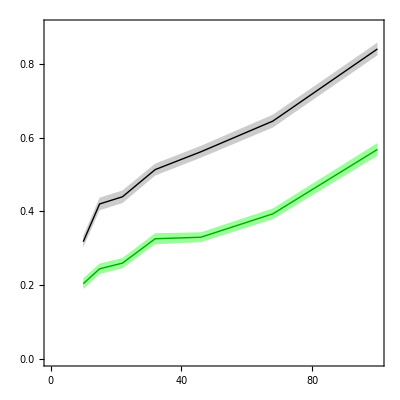

```mathematica
Show[ListLinePlot[{Partition[Riffle[contrastList,meanNormCRFBeforeV1axons],2],Partition[Riffle[contrastList,(meanNormCRFBeforeV1axons+semNormCRFBeforeV1axons)],2],Partition[Riffle[contrastList,(meanNormCRFBeforeV1axons-semNormCRFBeforeV1axons)],2]},PlotRange->{0,0.9},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,100,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick],ListLinePlot[{Partition[Riffle[contrastList,meanNormCRFAfterV1axons],2],Partition[Riffle[contrastList,(meanNormCRFAfterV1axons+semNormCRFAfterV1axons)],2],Partition[Riffle[contrastList,(meanNormCRFAfterV1axons-semNormCRFAfterV1axons)],2]},PlotRange->{0,0.9},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,100,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick],AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

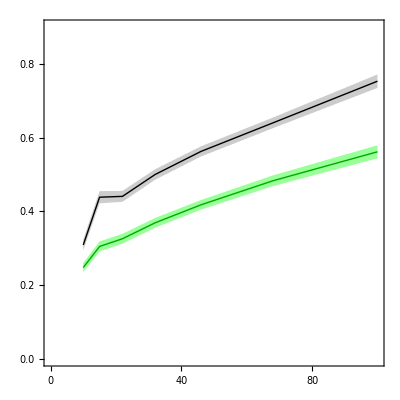

```mathematica
Show[ListLinePlot[{Partition[Riffle[contrastList,meanNormCRFBeforeLPaxons],2],Partition[Riffle[contrastList,(meanNormCRFBeforeLPaxons+semNormCRFBeforeLPaxons)],2],Partition[Riffle[contrastList,(meanNormCRFBeforeLPaxons-semNormCRFBeforeLPaxons)],2]},PlotRange->{0,0.9},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,100,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick],ListLinePlot[{Partition[Riffle[contrastList,meanNormCRFAfterLPaxons],2],Partition[Riffle[contrastList,(meanNormCRFAfterLPaxons+semNormCRFAfterLPaxons)],2],Partition[Riffle[contrastList,(meanNormCRFAfterLPaxons-semNormCRFAfterLPaxons)],2]},PlotRange->{0,0.9},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,100,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick],AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

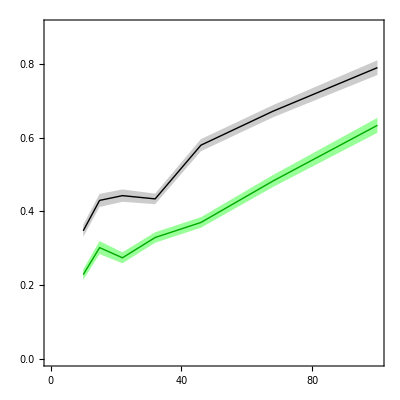

```mathematica
Show[ListLinePlot[{Partition[Riffle[contrastList,meanNormCRFBeforeLMaxons],2],Partition[Riffle[contrastList,(meanNormCRFBeforeLMaxons+semNormCRFBeforeLMaxons)],2],Partition[Riffle[contrastList,(meanNormCRFBeforeLMaxons-semNormCRFBeforeLMaxons)],2]},PlotRange->{0,0.9},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,100,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick],ListLinePlot[{Partition[Riffle[contrastList,meanNormCRFAfterLMaxons],2],Partition[Riffle[contrastList,(meanNormCRFAfterLMaxons+semNormCRFAfterLMaxons)],2],Partition[Riffle[contrastList,(meanNormCRFAfterLMaxons-semNormCRFAfterLMaxons)],2]},PlotRange->{0,0.9},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[0,100,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick],AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```